```mathematica
Monitor[Table[CalcVotedValuesSummaryForRangePure[Subsets[Prime[Range[2,last]], {2,last}], 16000], {last,13,14}], Prime[last]]
```

$Aborted

```mathematica
Streams[]
```

{OutputStream[stdout,1],OutputStream[stderr,2]}

```mathematica
Close[Streams[][[3]]]
```

d:\triangle\Votes\7\11\13\17\23\29\31\VotedValues.txt

```mathematica
Prime[14]
```

43

```mathematica
NextVote[primes_, start_] := Module[{   maxdist, distanceTable,  result},
result = start;
distanceTable = ParallelTable[Distance[result, p], {p, primes}];
maxdist = Max[distanceTable];
If[maxdist==0,
result +=1;
,
result += maxdist;
];
Return[result]
]
```

```mathematica
MeanBadPosition[vote_, tuple_] := Module[{},
Return[
Mean[
Table[
With [{digs=IntegerDigits[vote,p]},
N[Length[Select[digs,#>=(p+1)/2&]] / Length[digs]]
],
{p,tuple}
]
]
]
]
```

```mathematica
MeanBadPosition[100, {3,5,7}]
```

0.177778

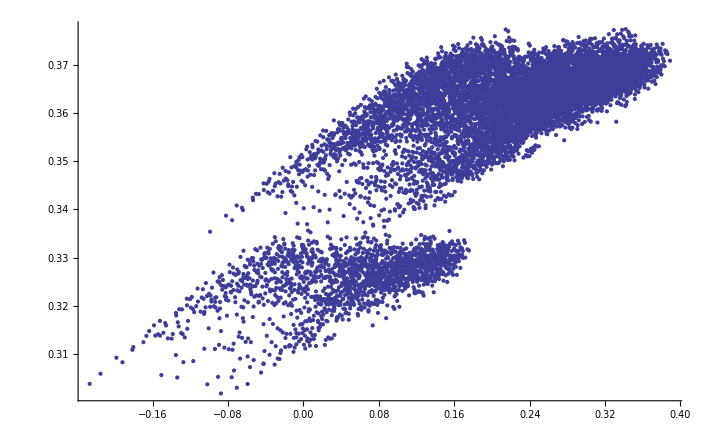

```mathematica
Monitor[
With [
{last = 25},
ListPlot[
Sort[
Table[
N[{magicGraham[tuple],MeanBadPosition[NextVote[tuple, 10^10000], tuple]}],
{tuple, Subsets[Prime[Range[2,last]], {4,4}]}
]
]
]
], 
 " - " <> ToString[tuple]
]
```

```mathematica
Prime[15]
```

47

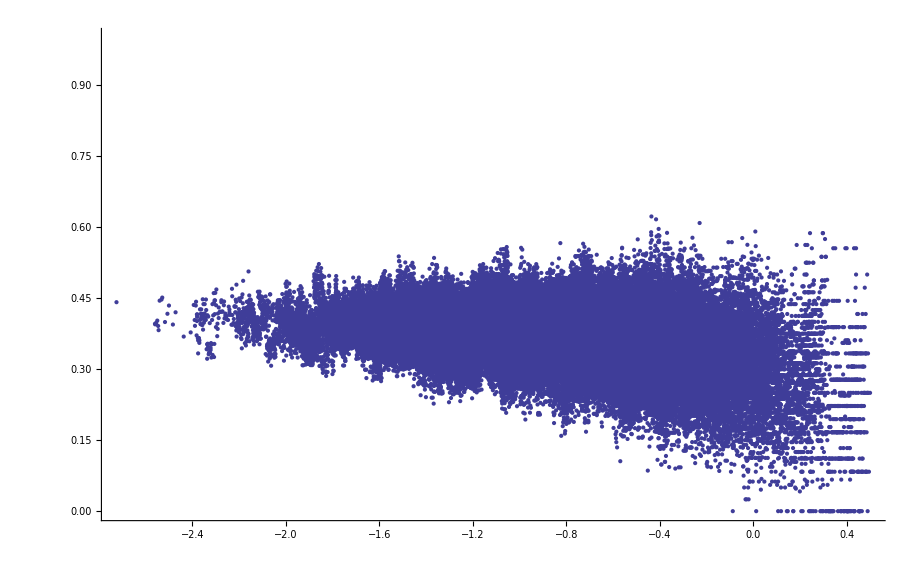

```mathematica
Monitor[
With [
{last = 18},
ListPlot[
Sort[
Table[
N[{magicGraham[tuple],MeanBadPosition[NextVote[tuple,Fold[Times,1,tuple]], tuple]}],
{tuple, Subsets[Prime[Range[2,last]], {3,last}]}
]
],
PlotRange->{All,{0,1}}
]
], 
 " - " <> ToString[tuple]
]
```

```mathematica
Fold[Times,1,{2,3}]
```

6

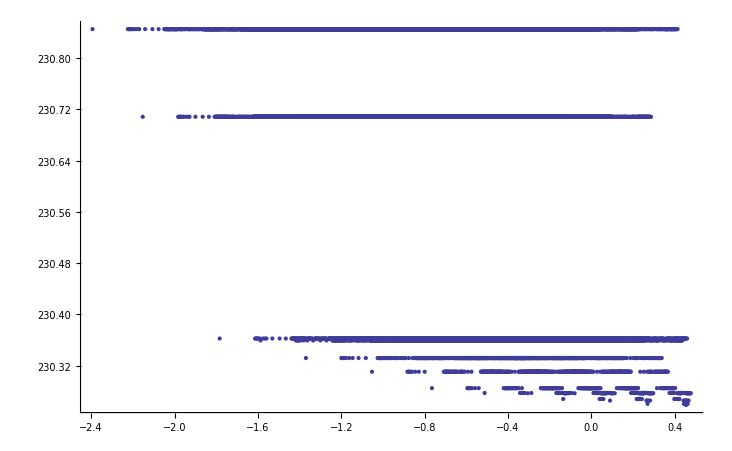

```mathematica
Monitor[
With [
{last = 16},
ListPlot[
Sort[
Table[
N[{magicGraham[tuple],Log[NextVote[tuple,10^100]]}],
{tuple, Subsets[Prime[Range[2,last]], {3,last}]}
]
]
]
], 
 " - " <> ToString[tuple]
]
```

```mathematica
With [
{last = 6},
Sort[
Table[
N[{magicGraham[tuple],Log[NextVote[tuple,10^10000]]}],
{tuple, Subsets[Prime[Range[2,last]], {3,last}]}
]
]
]
```

{{-0.468174,23026.2},{-0.226828,23026.2},{-0.215395,23026.2},{-0.180588,23026.2},{-0.15078,23026.},{-0.0991033,23026.2},{0.0259503,23026.2},{0.0607577,23026.2},{0.0721904,23026.2},{0.0905659,23026.},{0.101999,23026.},{0.136806,23026.},{0.142242,23026.2},{0.153675,23026.2},{0.188482,23026.2},{0.218291,23026.}}